```mathematica
Clear[a]
```



```mathematica
Plot[Sin[x],{x,0,2π}]
```

```mathematica
Manipulate[
Plot[Sin[frequency*x],{x,0,2π}],
{frequency,1,5}]
```

```mathematica
Manipulate[Plot[Sin[frequency x],{x,0,2 π}],{frequency,1,5},AutoAction->True]
```

```mathematica
Manipulate[
Plot[
Sin[frequency*x+phase],{x,0,2π}],
{frequency,1,5},
{phase,0,10}]
```

```mathematica
Manipulate[
Plot[
function[frequency*x+phase],{x,0,2π}],
{frequency,1,5},
{phase,0,10},
{function,{Sin,Cos,Tan}}]
```

```mathematica
Manipulate[
Plot[
function[frequency*x+phase],{x,0,2π}],
{frequency,1,5},
{phase,0,10},
{function,{Sin,Cos,Tan,Csc,Sec,Cot}}]
```

```mathematica
Manipulate[
Plot[
function[frequency*x+phase],{x,0,2π}],
{frequency,1,5},
{phase,0,10},
{function,{Sin,Cos,Tan,Csc,Sec,Cot},ControlType->RadioButtonBar}]
```

```mathematica
Manipulate[Expand[(a+b)^n],
{n,2,10,1}]
```

```mathematica
Manipulate[
Plot[a*Sin[x],{x,0,2π},
PlotRange->{-11,11}],
{a,1,10}]
```

```mathematica
Manipulate[
Plot3D[Sin[a x y],{x,-2,2},{y,-2,2}],
{a,1,5}]
```

```mathematica
Manipulate[
Plot3D[Sin[a x y],{x,-2,2},{y,-2,2},PerformanceGoal->"Quality"],
{a,1,5}]
```

Using Performance goal “Quality” allows to have smoother visualizations when manipulating the view.

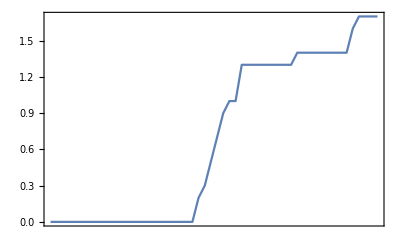

```mathematica
DateListPlot[WeatherForecastData[Entity["City",{"Chisinau","Chisinau","Moldova"}], "PrecipitationAmount", UnitSystem->"Metric"]]
```

```mathematica
EntityClass["NuclearExplosion","BelowSea"]
```

under-sea nuclear explosions

```mathematica
CommonName[EntityClass["NuclearExplosion","BelowSea"]]
```

under-sea nuclear explosions

WolframAlphaQueryParseResults

```mathematica
Entity["NuclearExplosion","UnitedStates08091945"]["Dataset"]
```

WolframAlphaQueryParseResults

```mathematica
Entity["NuclearExplosion","NorthKorea09092016"]["Dataset"]
```

WolframAlphaQueryResults

```mathematica
{{{{"nuclear explosions", "local map"}}}}
```

nuclear explosions | local map

```mathematica
EntityClass["NuclearExplosion", {"Latitude"-> TakeSmallest[5]}]//EntityList
```

{Argus II,Argus III,Argus I,Antler Round 3,Buffalo R4}

```mathematica
Manipulate[
Plot[fn[f*x+ps], {x, 0,2π}],
{{f, 1, "frequency"},1,5},
{{ps, 0, "phase shift"},0,10},
{{fn, Sin, "function"}, {Sin,Cos,Tan,Csc,Sec,Cot}}]
```

```mathematica
Manipulate[
Plot[fn[f*x+ps], {x, 0,2π}],
{{f, 1, "frequency"},1,5, Appearance-> "Labeled"},
{{ps, 0, "phase shift"},0,10, Appearance-> "Labeled"},
{{fn, Sin, "function"}, {Sin,Cos,Tan,Csc,Sec,Cot}}]
```

```mathematica
Manipulate[
Plot[Sin[f*x],{x,0,2π}],
{{f,1,"frequency"},1,5,Appearance->"Labeled"}]
```

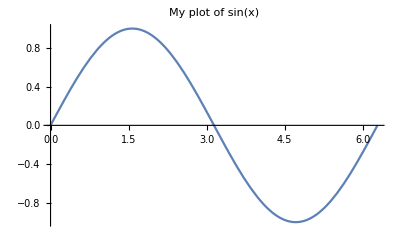

```mathematica
Plot[Sin[x],{x,0,2π}, PlotLabel->"My plot of sin(x)"]
```

```mathematica
Plot[Sin[x],{x,0,2π}, PlotLabel->"My plot of "<>"sin(x)"]
```

-Graphics-

```mathematica
Manipulate[
Plot[Sin[f*x],{x,0,2π},PlotLabel->"sin("<>ToString[f]<>"x)"],
{{f,1,"frequency"},1,5,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Plot[Sin[f*x+ ps],{x,0,2π},
PlotLabel->"sin("<>ToString[f]<>"x+ "<>ToString[ps]<>")"],
{{f,1,"frequency"},1,5,Appearance->"Labeled"},
{{ps,1,"phase shift"},1,6, Appearance->"Labeled"}]
```

```mathematica
f[x_]:= 2 x^2+2x+1
```

```mathematica
Manipulate[
Plot[f[a*x],{x,-4,4},PlotRange->{0,25}],
{a,-1,1}]
```

```mathematica
Manipulate[
Plot[f[a*x],{x,-4,4},PlotRange->{0,25}],
{a,-1,1},
SaveDefinitions->True]
```

## Exercises

```mathematica
Manipulate[
Plot[a*x^2+1,{x,1,10}],
{a,-1,1, Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Plot[a*{x,x^2+1, x^3+1},{x,1,10}],
{a, -1, 1, Appearance->"Labeled"} ]
```

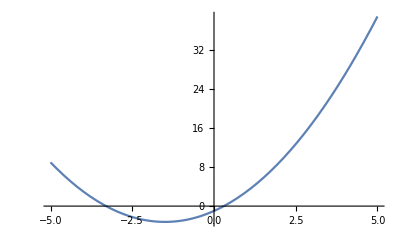

```mathematica
Plot[x^2+3x-1,{x,-5,5}]
```

```mathematica
Manipulate[
Plot[c x^2+3x-1,{x,-5,5}, PlotRange->{-5,100}],
{c, 1, 20, Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Plot[c x^2+3d x-1,{x,-5,5}, PlotRange->{-5,100}],
{c, 1, 20, Appearance->"Labeled"},
{d, 0, 20, Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Plot[{c x^2+3d x-1,2c x^2+3d x-1},{x,-5,5}, PlotRange->{-5,100}],
{c, 1, 20, Appearance->"Labeled"},
{d, 0, 20, Appearance->"Labeled"}]
```

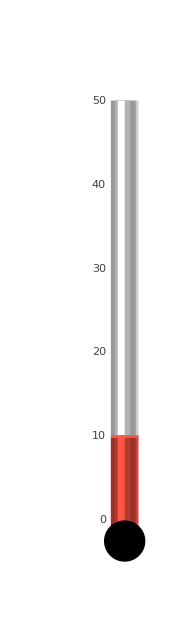

```mathematica
ThermometerGauge[10,{0,50}]
```

```mathematica
Manipulate[
ThermometerGauge[10x, {0,50}],
{x,0,5, Appearance->"Labeled"}]
```